## Notes

-0400->-4

timezone [num_String] := "GMT-" + num[-3]

StringJoin

## Inputting Data from File

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Connie\Downloads\Summer2018Starter-master\Summer2018Starter-master\Summer2018

```mathematica
heartRate= Import["HKQuantityTypeIdentifierHeartRate.csv","CSV"];
```

```mathematica
getImportantData[ entries_List ]:= Part[ entries , All, -1];

(* hjhhkh *)
getDateString[ entry_String ]:= Part [ StringSplit[ entry ,";"] , -2] ;

(* gets heart rate value as a Number *)
getHeartRate[ entry_String ]:= ToExpression [Part [ StringSplit[ entry ,";"] , -1]] ;
```

```mathematica
getDateString ["software:3.1>;count/min;2017-02-06 20:00:03 -0400;2017-02-06 19:58:53 -0400;2017-02-06 19:58:53 -0400;61"]
```

{software:3.1>,count/min,2017-02-06 20:00:03 -0400,2017-02-06 19:58:53 -0400,2017-02-06 19:58:53 -0400,61}

Dropping the first line, extract all rows and columns of heartrate data

```mathematica
getImportantData[Drop[heartRate,1]]
```

{software:3.1>;count/min;2017-02-06 20:00:03 -0400;2017-02-06 19:58:53 -0400;2017-02-06 19:58:53 -0400;61,257626,software:4.3.1>;count/min;2018-07-04 14:30:46 -0400;2018-07-04 14:25:36 -0400;2018-07-04 14:25:36 -0400;71}
 |  |  |  |

get time entry from ”2017-02-06 20:00:03 -0400”  in correct format and replace 4 digit num. for time zone with form: GMT-4        stringjoin with “GMT -“ + num[-3]

```mathematica
getDateObject[ timeEntry_String ] := 
                                    With[ { extractTZ = StringTake[ timeEntry , {-5,-1} ] },
                                    
                                           timeZoneString = StringJoin[" GMT-", ToString[ (Interpreter["Number"][StringTake[extractTZ,{2,3}]])] ];
                                           
                                           DateObject[ StringDrop[ timeEntry , -5]
                                                         ]
                                         ];
                                         
  
  getAllDateObjects [  entries_List ] := Map [ 
                                                 getDateObject[ 
                                                                getDateString [ # ]
                                                              ] &
                                                   ,
                                                   getImportantData[ entries ]
                                               ];
                                                   
 
  getAllHeartPoints [  entries_List ] := Map [  
                                                getHeartRate
                                                , 
                                                getImportantData[ entries ] 
                                              ] ;
```

```mathematica
Map [Style[ToString [#],Italic]& , {1,2,3,4}]
```

{1,2,3,4}

```mathematica
getAllDateObjects [Drop[heartRate,1]]
```

{Mon 6 Feb 2017 19:58:53GMT-4.,Mon 6 Feb 2017 20:03:21GMT-4.,Mon 6 Feb 2017 20:06:30GMT-4.,Mon 6 Feb 2017 20:12:08GMT-4.,257620,Wed 4 Jul 2018 14:11:05GMT-4.,Wed 4 Jul 2018 14:16:59GMT-4.,Wed 4 Jul 2018 14:22:11GMT-4.,Wed 4 Jul 2018 14:25:36GMT-4.}
 |  |  |  |

```mathematica
heartRatePoints = getAllHeartPoints [ Drop[heartRate,1]]
```

{61,60,58,61,55,53,52,51,49,49,49,49,49,49,51,51,52,53,54,54,54,59,61,51,51,51,50,51,52,52,53,53,49,51,54,52,53,52,49,49,49,52,53,51,51,51,52,58,257532,65,65,63,65,60,64,65,70,65,62,69,59,72,69,62,68,57,57,68,64,63,62,63,66,71,66,76,70,68,77,94,81,80,68,67,79,83,75,81,82,69,71,77,79,68,75,70,71}
 |  |  |  |

```mathematica
Transpose[{{"m","t","W"},{1,24,1}}]
```

{{m,1},{t,24},{W,1}}

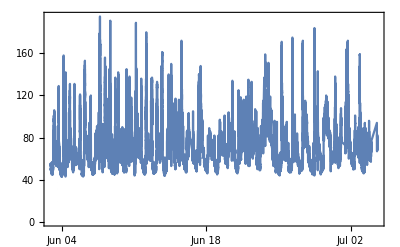

```mathematica
DateListPlot [ Take[Transpose[{dateObjects,heartRatePoints}],-25000]]
```

```mathematica
dateObjects= %131 ;
```

```mathematica
dateObjects [[1]]
```

Mon 6 Feb 2017 19:58:53GMT-4.

```mathematica
SetDirectory[NotebookDirectory []]
```

C:\Users\Connie\Downloads\Summer2018Starter-master\Summer2018Starter-master\Summer2018

```mathematica
Export ["DateObject.mx", dateObjects ,"MX" ]
```

DateObject.mx

```mathematica
dobjs=Import["DateObject.mx"];
```

```mathematica
getTimePoint["2017-02-06 20:00:03-0400"]
```

Mon 6 Feb 2017 20:00:03GMT-4

```mathematica
getAllDateObjects[]
```

```mathematica
?DateObject
```

DateObject[] gives the current local date.
DateObject[{y,m,d,h,m,s}] gives a date object of standard normalized form.
DateObject[string] converts a date string to a date object.
DateObject[{string,{e_1,e_2, …}}] gives the date object obtained by extracting elements "e_i" from "string".
DateObject[rdate,gran] gives the date object of calendar granularity gran that includes the reference date rdate.

```mathematica
extractTZ=StringTake["2017-02-06 20:00:03-0400" ,{-5,-1}];
DateObject[StringJoin[StringDrop[ "2017-02-06 20:00:03-0400" , -5]," GMT-", ToString@Interpreter["Number"][StringTake[extractTZ,{2,3}]]]]
```

DateObject::str: String 2017-02-06 20:00:03 GMT-4 cannot be interpreted as a date.

```mathematica
extractTZ=StringTake["2017-02-06 20:00:03-0400" ,{-5,-1}];
DateObject[StringJoin[StringDrop[ "2017-02-06 20:00:03-0400" , -5]," GMT-", ToString@Interpreter["Number"][StringTake[extractTZ,{2,3}]]]]
```

DateObject::str: String 2017-02-06 20:00:03 GMT-4 cannot be interpreted as a date.

DateObject[2017-02-06 20:00:03 GMT-4]

```mathematica
DateObject
```

```mathematica
DateObject[StringDrop[ "2017-02-06 20:00:03-0400" , -5],TimeZone->Interpreter["TimeZone"][StringJoin[" GMT-", ToString@Interpreter["Number"][StringTake[extractTZ,{2,3}]]]]]
```

Mon 6 Feb 2017 20:00:03GMT-4

## Extracting Useful Data

```mathematica
valueColumn = heartRate[All,-1];
timeColumn     = heartRate[All,-2];
```

```mathematica
StringSplit[
Part[{"software:3.1>","count/min","2017-02-06 20:00:03 -0400","2017-02-06 19:58:53 -0400","2017-02-06 19:58:53 -0400","61"},-2]
]
StringJoin[{"2017-02-06","19:58:53","-0400"}," "]
```

DateObject[StringDrop[
StringSplit[
Part[{“software:3.1>”,”count/min”,”2017-02-06 20:00:03 -0400”,”2017-02-06 19:58:53 -0400”,”2017-02-06 19:58:53 -0400”,”61”},-2]
,” “]
, -6]]

## Calibrating and Formatting of Data for Analysis

```mathematica
Interpreter["Location"]["Barcelona"]
```

GeoPosition[{41.4,2.17}]